## TB NNN

```mathematica
Quit
```

```mathematica
(*https://lampz.tugraz.at/~hadley/ss1/crystalstructure/structures/hcp/hcp.php*)
```

```mathematica
(*Lattice constant*)
a=1.49;    (*look for papers that show this value (angstrom).*)
t=2.7;                            (*t=2.7–2.9 (eV;2.7 is common)*)
Δ=0;
t2A =0.2;(*look for papers that show this value 0.1*)
t2B =0.2;
(*Δ=0 for graphene and Δ=5.8 for hBN. t=2.9 graphene and t=2.7. a=2.46 for graphene*)
(*Real-space lattice vectors*)
a1=a*{3/2,-Sqrt[3]/2};
a2=a*{3/2,Sqrt[3]/2};
```

```mathematica
(*I can also use a1=a*{3/2,-Sqrt[3]/2};
a2=a*{3/2,Sqrt[3]/2}; but a should be here the nn distance or the bond distance*)
```

```mathematica
(*Compute area of unit cell*)
area=a1[[1]]*a2[[2]]-a1[[2]]*a2[[1]];
```

```mathematica
b1=(2*Pi/area)*{a2[[2]],-a2[[1]]};
b2=(2*Pi/area)*{-a1[[2]],a1[[1]]};
```

```mathematica
delta1=(a1+a2)/3;
delta2=(-2*a1/3+a2/3);
delta3=(a1/3-2*a2/3);
delta4=a1;
delta5=a2;
delta6=-a1;
delta7 = -a2;
delta8=(a2-a1);
delta9=-(a2-a1);
```

```mathematica
gamma[kx_,ky_]:=Exp[I*(kx*delta1[[1]]+ky*delta1[[2]])]+Exp[I*(kx*delta2[[1]]+ky*delta2[[2]])]+Exp[I*(kx*delta3[[1]]+ky*delta3[[2]])]
```

```mathematica
gk[kx_,ky_]:=2 (Cos[kx a1[[1]]+ky a1[[2]]]+Cos[kx a2[[1]]+ky a2[[2]]]+Cos[kx (a2-a1)[[1]]+ky (a2-a1)[[2]]]);
```

```mathematica
H[kx_,ky_]:={{Δ/2+t2A*gk[kx,ky],t*gamma[kx,ky]},{t*Conjugate[gamma[kx,ky]],-Δ/2+t2B*gk[kx,ky]}};
```

```mathematica
eigenvals[kx_,ky_]:=Sort[Eigenvalues[H[kx,ky]]]
```

```mathematica
kΓ={0,0};
kK=(1/3)*(b1-b2)
kM=(1/2)*b1;
```

{0.,-1.62309}

```mathematica
gamma[0.,-1.6230866794042216]
```

3.88578×10^-16+0. ⅈ

```mathematica
eigenvals[0.,-1.6230866794042216]
```

{-0.45,-0.45}

```mathematica
(*gamma*)
```

```mathematica
gk[0,0]
```

6.

```mathematica
gamma[0,0]
```

3.+0. ⅈ

```mathematica
(*K*)
```

```mathematica
gk[0.,-1.6230866794042216]
```

-3.

```mathematica
gamma[0.,-1.6230866794042216]
```

3.88578×10^-16+0. ⅈ

```mathematica
(*M*)
```

```mathematica
gk[0.7028171484540925,-1.2173150095531662]
```

-2.

```mathematica
(*at M is complex so i just have to take the absolute value*)
```

```mathematica
gamma[0.7028171484540925,-1.2173150095531662]
```

0.5+0.866025 ⅈ

```mathematica
Abs[gamma[0.7028171484540925,-1.2173150095531662]]
```

1.

## PLOT Vectors

```mathematica
(*6 Nearest neighboor at a distance delta4*)
```

```mathematica
delta4=a1;
delta5=a2;
delta6=-a1;
delta7 = -a2;
delta8=(a2-a1);
delta9=-(a2-a1);
```

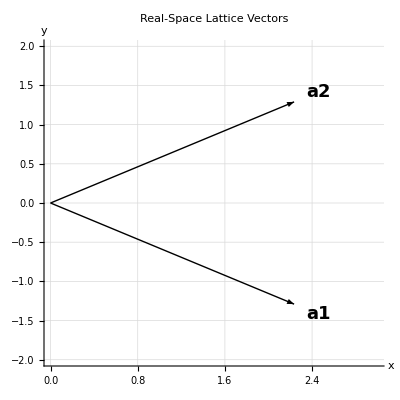

```mathematica
(*----Plot Primitive vectors 60-degree primitive-vector convention----*)

realVectors=Graphics[{
(*Plot lattice vectors*)
Arrow[{{0,0},a1}],Text[Style["a1",18,Bold],1.1 a1,{0,-1}],
Arrow[{{0,0},a2}],Text[Style["a2",18,Bold],1.1 a2,{0,1}]},
Axes->True,AxesLabel->{"x","y"},
PlotRange->{{0,3},{-2,2}},
GridLines->Automatic,AspectRatio->1,PlotLabel->Style["Real-Space Lattice Vectors",18],LabelStyle->14];GraphicsRow[{realVectors}]
```

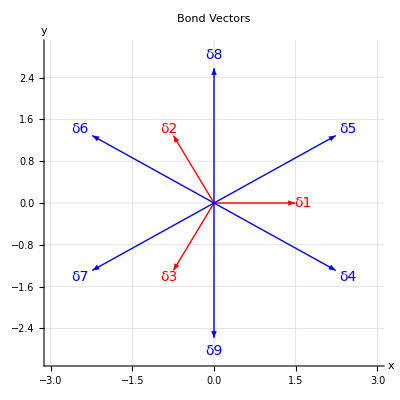

```mathematica
(*----Plot Real Space Vectors----*)

realVectors=Graphics[{
(*Plot delta vectors*)
Red,
Arrow[{{0,0},delta1}],Text[Style["δ1",14],1.1*delta1,{-1,0}],
Arrow[{{0,0},delta2}],Text[Style["δ2",14],1.1*delta2,{1,0}],
Arrow[{{0,0},delta3}],Text[Style["δ3",14],1.1*delta3,{-1,0}],
Blue,
Arrow[{{0,0},delta4}],Text[Style["δ4",14],1.1*delta4,{-1,0}],
Arrow[{{0,0},delta5}],Text[Style["δ5",14],1.1*delta5,{-1,0}],
Arrow[{{0,0},delta6}],Text[Style["δ6",14],1.1*delta6,{-1,0}],
Arrow[{{0,0},delta7}],Text[Style["δ7",14],1.1*delta7,{-1,0}],
Arrow[{{0,0},delta8}],Text[Style["δ8",14],1.1*delta8,{-1,0}],
Arrow[{{0,0},delta9}],Text[Style["δ9",14],1.1*delta9,{-1,0}]},
Axes->True,AxesLabel->{"x","y"},
PlotRange->{{-3,3},{-3,3}},
GridLines->Automatic,AspectRatio->1,PlotLabel->"Bond Vectors",LabelStyle->14];GraphicsRow[{realVectors}]
```

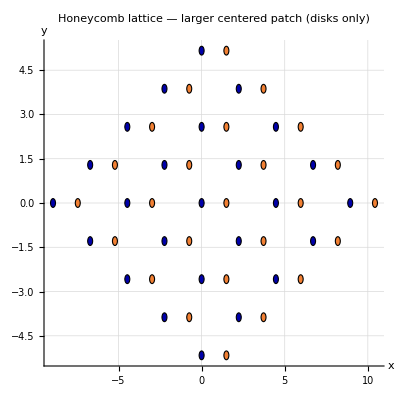

```mathematica
(*Uses your existing a1,a2,and delta1..delta3.No arrows,just disks.*)(*how many unit cells along each direction*)NX=5;   (*along a1*)
NY=5;   (*along a2*)

(*disk radius from the nearest-neighbor bond length*)
ballR=0.1*Norm[delta1];

(*build the NX x NY supercell and center it around the origin*)
cells=Flatten[Table[{i,j},{i,0,NX-1},{j,0,NY-1}],1];
translations=(#[[1]]*a1+#[[2]]*a2)&/@cells;

centerShift=((NX-1)/2)*a1+((NY-1)/2)*a2;

Bshift=delta1;  (*you can switch to delta2 or delta3 if you prefer*)
Apoints=(#-centerShift)&/@translations;
Bpoints=(#+Bshift-centerShift)&/@translations;

bigPatch=Graphics[{{Darker[Blue],EdgeForm[Black],(Ball[#,ballR]&/@Apoints)},(*A sublattice*){RGBColor[0.95,0.5,0.2],EdgeForm[Black],(Disk[#,ballR]&/@Bpoints)}  (*B*)},Axes->True,AxesLabel->{"x","y"},AspectRatio->1,GridLines->Automatic,PlotRange->All,PlotLabel->"Honeycomb lattice — larger centered patch (disks only)"];

bigPatch
```

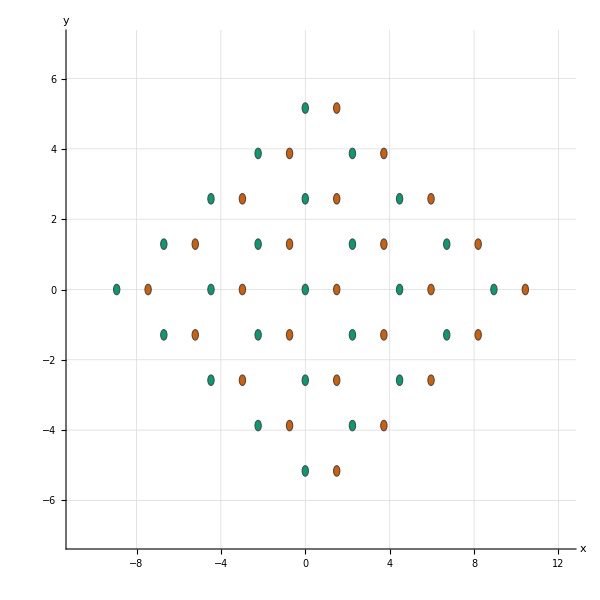

```mathematica
(*how many unit cells along each direction*)
NX=5;   (*along a1*)
NY=5;   (*along a2*)

(*disk radius from the nearest-neighbor bond length*)
ballR=0.10*Norm[delta1];

(*build the NX×NY supercell and center it around the origin*)
cells=Flatten[Table[{i,j},{i,0,NX-1},{j,0,NY-1}],1];
translations=(#[[1]]*a1+#[[2]]*a2)&/@cells;
centerShift=((NX-1)/2)*a1+((NY-1)/2)*a2;

Bshift=delta1;  (*choose delta1/delta2/delta3 as you like*)
Apoints=(#-centerShift)&/@translations;
Bpoints=(#+Bshift-centerShift)&/@translations;

(*nice,muted styling*)
colA=RGBColor[0.000,0.620,0.451];   (*A sublattice*)
colB=RGBColor[0.835,0.369,0.000];   (*B sublattice*)
eCol=GrayLevel[0.3];

(*square,padded plot range so disks stay circular*)
allPts=Join[Apoints,Bpoints];
{xmin,xmax}=MinMax[allPts[[All,1]]];
{ymin,ymax}=MinMax[allPts[[All,2]]];
pad=0.1*Max[xmax-xmin,ymax-ymin];
xrng={xmin-pad,xmax+pad};
yrng={ymin-pad,ymax+pad};

bigPatch=Graphics[{{EdgeForm[Directive[eCol,Thin]],colA,Disk[#,ballR]}&/@Apoints,{EdgeForm[Directive[eCol,Thin]],colB,Disk[#,ballR]}&/@Bpoints},PlotRange->{xrng,yrng},AspectRatio->1,ImageSize->600,Background->White,Axes->True,AxesLabel->(Style[#,13]&/@{"x","y"}),GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[.92]],TicksStyle->Directive[GrayLevel[.3],11],PlotLabel->Style["",14]];

bigPatch
```

```mathematica
Export["/Users/greis/Library/CloudStorage/OneDrive-StateUniversityofNewYorkatNewPaltz/2025-II/Undergrad-Research/Flavio/A-B-Sublattices.eps",%194,"EPS"]
```

/Users/greis/Library/CloudStorage/OneDrive-StateUniversityofNewYorkatNewPaltz/2025-II/Undergrad-Research/Flavio/A-B-Sublattices.eps

## PLOT Band Structure

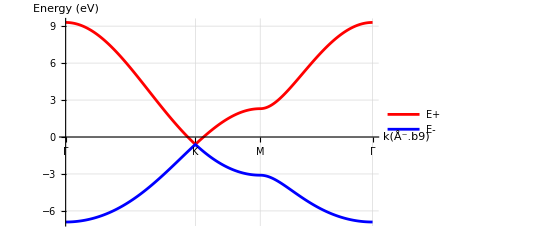

```mathematica
area=a1[[1]]*a2[[2]]-a1[[2]]*a2[[1]];
b1=(2*Pi/area)*{a2[[2]],-a2[[1]]};
b2=(2*Pi/area)*{-a1[[2]],a1[[1]]};

kΓ={0,0};
kK=(1/3)*(b1-b2);
kM=(1/2)*b1;
kPath=Join[Table[(1-s) kΓ+s kK,{s,0,1,0.01}],Table[(1-s) kK+s kM,{s,0,1,0.01}],Table[(1-s) kM+s kΓ,{s,0,1,0.01}]];
kDistances=
Prepend[
Accumulate[
Norm/@Differences[kPath]
],
0
];
bands=eigenvals@@@kPath;
bandsPlus=bands[[All,2]];
bandsMinus=bands[[All,1]];
symmetryPoints={1,Length[kPath]/3,2*Length[kPath]/3,Length[kPath]};
tickPositions=kDistances[[Round[symmetryPoints]]];
tickLabels={"Γ","K","M","Γ"};
ticks=Transpose[{tickPositions,tickLabels}];
bandsPlusData=Transpose[{kDistances,bandsPlus}];
bandsMinusData=Transpose[{kDistances,bandsMinus}];
Show[ListLinePlot[bandsPlusData,Joined->True,PlotStyle->Red,PlotLegends->{"E+"}],ListLinePlot[bandsMinusData,Joined->True,PlotStyle->Blue,PlotLegends->{"E-"}],Ticks->{{{kDistances[[1]],"Γ"},{kDistances[[Length[kPath]/3]],"K"},{kDistances[[2*Length[kPath]/3]],"M"},{kDistances[[Length[kPath]]],"Γ"}},Automatic},AxesLabel->{"k(Å⁻.b9)","Energy (eV)"},GridLines->Automatic,PlotLabel->Style["",16],PlotRange->All,LabelStyle->14]
```

## Band structure vs t2

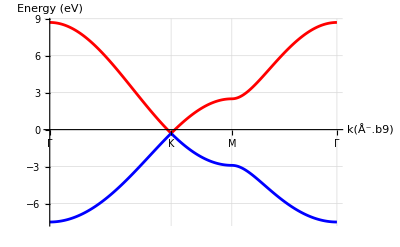
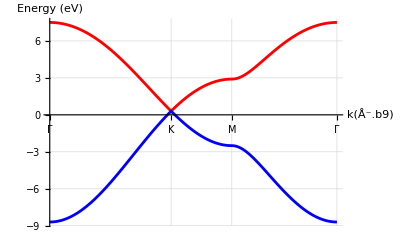
t2=0.1
-Graphics-
t2=-0.1
-Graphics-

t2 = -0.2

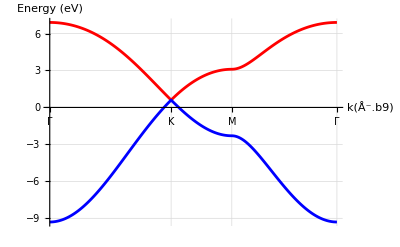

t2 = 0.2

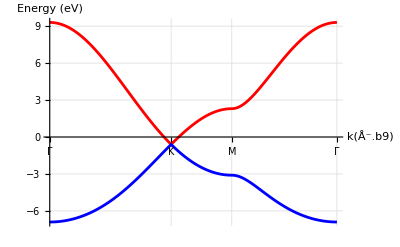

## TB+Heat Map A(k)

```mathematica
Quit
```

```mathematica
(* =========================Graphene heat map with K/K' labels Bond-length convention (a=nearest-neighbor distance)=========================*)(*---1) Geometry:real space (60-degree primitives)---*)
a=1.42;                                 (*bond length in angstrom*)
a1=a*{3/2,-Sqrt[3]/2};
a2=a*{3/2,Sqrt[3]/2};

(*nearest neighbors (A->B),each has length a*)
delta1=(a1+a2)/3;
delta2=(-2 a1+a2)/3;
delta3=(a1-2 a2)/3;

(*---2) Reciprocal lattice---*)
area=Det[{a1,a2}];                      (* =(3 Sqrt[3]/2) a^2*)
b1=(2 Pi/area) {a2[[2]],-a2[[1]]};
b2=(2 Pi/area) {-a1[[2]],a1[[1]]};

(*---3) Structure factors---*)
gamma[kx_,ky_]:=Module[{k={kx,ky}},Exp[I k.delta1]+Exp[I k.delta2]+Exp[I k.delta3]];
gk[kx_,ky_]:=Module[{k={kx,ky}},2 (Cos[k.a1]+Cos[k.a2]+Cos[k.(a2-a1)])];

(*---4) High-symmetry points and BZ hexagon---*)
(*six corners generated from three representatives and their negatives*)
K1=(2 b1+b2)/3;          (*three inequivalent corners*)
K2=(b1+2 b2)/3;
K3=(b1-b2)/3;

Ks={K1,-K2,-K3};        (*label these as K*)
Kps={K2,-K1,K3};         (*label these as K'*)

Γpt={0.,0.};

(*order the six corners counterclockwise to draw the hexagon outline*)
allCorners={K1,K2,K3,-K1,-K2,-K3};
orderAngle[p_]:=ArcTan[p[[1]],p[[2]]];
hex=SortBy[allCorners,orderAngle]//N;
hex=Append[hex,First@hex];           (*close the loop*)

(*---5) Tight plot box around the hexagon with a small padding---*)
xmin=Min[hex[[All,1]]];xmax=Max[hex[[All,1]]];
ymin=Min[hex[[All,2]]];ymax=Max[hex[[All,2]]];
pad=0.10 Max[xmax-xmin,ymax-ymin];
xrng={xmin-pad,xmax+pad};
yrng={ymin-pad,ymax+pad};

(*---6) Uniform sampling grid in that rectangle---*)
nx=201;ny=201;
xs=Subdivide[xrng[[1]],xrng[[2]],nx-1];
ys=Subdivide[yrng[[1]],yrng[[2]],ny-1];

(*---7) Helper for outward label offset from Γ---*)
offVec[pt_,Γ_:{0.,0.},r_:0.07]:=If[Norm[pt-Γ]<10^-12,{r,r},r Normalize[pt-Γ]];

(*make sure gk is defined (and that a1,a2 exist)*)
```

```mathematica
t2A=-0.1;t2B=-0.1;t2sum=t2A+t2B;
t2sumMax=0.30;zmin=-9 t2sumMax;zmax=9 t2sumMax;
Adata=Flatten[Table[{x,y,t2sum*(gk[x,y]+3)},{x,xs},{y,ys}],1];

cf=(ColorData["SolarColors"][Rescale[#,{zmin,zmax}]]&);

ListDensityPlot[Adata,ColorFunction->cf,ColorFunctionScaling->False,PlotRange->{xrng,yrng,{zmin,zmax}},Epilog->{{Thickness[0.002],Black,Line[hex]},{PointSize[0.018],Black,Point[Γpt],Text[Style["Γ",14,Bold],Γpt+{0.06,0.06}]},(*paste K/K' blocks here*)Table[With[{p=N@pt,off=0.07 Normalize[pt-Γpt]},{PointSize[0.016],Black,Point[p],Text[Style["K",14,Bold],p+off]}],{pt,Ks}]//Sequence,Table[With[{p=N@pt,off=0.07 Normalize[pt-Γpt]},{PointSize[0.016],Black,Point[p],Text[Style["K′",14,Bold],p+off]}],{pt,Kps}]//Sequence},PlotLegends->BarLegend[{"SolarColors",{zmin,zmax}},LegendLabel->"A(k) = (t2A + t2B) g(k) (electronvolt)"]]
```

-Graphics-

```mathematica
t2sum:=t2A+t2B;
Arel[x_,y_]:=t2sum (gk[x,y]+3);     (*zero at K/K'*)
Avals=Flatten@Table[Arel[x,y],{x,xs},{y,ys}];
asymScore=Max[Avals];                   (* =9|t2sum|*)
asymScoreN=asymScore/(9 Max[Abs[t2sum],10^-12])  (*normalized:0..1*)
```

-0.0000235074

```mathematica
t2sum:=t2A+t2B;
Arel[kx_,ky_]:=t2sum (gk[kx,ky]+3);
kM=(1/2)*b1;
kK=(1/3)*(b1-b2);
(*at a single k0*)
k0={kM[[1]],kM[[2]]};
score=Abs@Arel@@k0;
scoreN=Abs[gk@@k0+3]/9

(*averaged over a small disk of radius r around k0*)
r=0.05;ns=121;
neigh=Table[k0+r {Cos[θ],Sin[θ]} ρ,{ρ,0,1,1./(Sqrt[ns]-1)},{θ,0,2 Pi,2 Pi/(Sqrt[ns]-1)}]//Flatten[#,1]&;
scoreAvg=Mean[Abs@*(Arel@@#&)/@neigh];
scoreNAvg=Mean[Abs[(gk@@#)+3]/9&/@neigh];
```

0.111111

In ARPES you see electron–hole asymmetry not by changing photon energy, but by showing that the upper and lower bands bend differently at equal energy distance from the Dirac point. In angle-resolved photoemission spectroscopy (ARPES), you shine photons and eject occupied electrons. The map shows band energy versus in-plane momentum from the states that already have electrons.

Changing photon energy does not switch between “electrons” and “holes.”
“Holes” are just the missing electrons below the Fermi level in the same ARPES image. You do not need a different photon energy to see them.To view the conduction band (which is unoccupied in undoped graphene), you must populate it (gating or chemical dosing) or use a pump–probe method (time-resolved ARPES). precise Dirac-point calibration is the experimental step that enables a clean, apples-to-apples curvature comparison where the asymmetry becomes evident.

What photon energy really changes:

0.111111

```mathematica
Quit
```

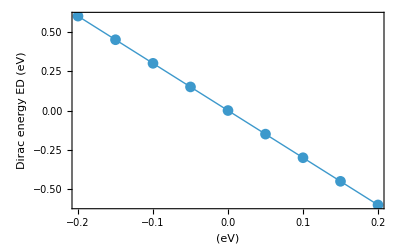

```mathematica
ED[t2A_,t2B_]:=-3 (t2A+t2B)/2;

t2vals=Range[-0.20,0.20,0.05];    (*eV*)
dataED=Table[{t2,ED[t2,t2]},{t2,t2vals}];   (*graphene:t2A=t2B=t2*)

ListLinePlot[dataED,Frame->True,FrameLabel->{" (eV)","Dirac energy ED (eV)"},PlotMarkers->Automatic,PlotStyle->Thick,LabelStyle->14]
```

```mathematica
(*once:fixed scale+color function*)
t2sumMax=0.20;
zmin=-9 Abs[t2sumMax];
zmax=9 Abs[t2sumMax];
cf=(ColorData["SunsetColors"][Rescale[#,{zmin,zmax}]]&);

plotT2[v_]:=(t2A=v/2;t2B=v/2;t2sum=v;
Adata=Flatten[Table[{x,y,t2sum*(gk[x,y]+3)},{x,xs},{y,ys}],1];
ListDensityPlot[Adata,ColorFunction->cf,ColorFunctionScaling->False,PlotRange->{xrng,yrng,{zmin,zmax}},PlotLegends->BarLegend[{cf,{zmin,zmax}},LabelStyle->14],Epilog->{{Thickness[0.002],Black,Line[hex]},{PointSize[0.018],Black,Point[Γpt],Text[Style["Γ",14],Γpt+{0.06,0.06}]},(*paste K/K' blocks here*)Table[With[{p=N@pt,off=0.07 Normalize[pt-Γpt]},{PointSize[0.016],Black,Point[p],Text[Style["K",14],p+off]}],{pt,Ks}]//Sequence,Table[With[{p=N@pt,off=0.07 Normalize[pt-Γpt]},{PointSize[0.016],Black,Point[p],Text[Style["K′",14],p+off]}],{pt,Kps}]//Sequence},PlotLabel->Row[{"= ",NumberForm[v,{3,2}]," eV"}],ImageSize->350]);

Row[plotT2/@{0.00,0.1,-0.1,0.20,-0.20}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(*asymmetric case- A and B different*)
```

```mathematica
plotT2pair[a_,b_]:=(t2A=a;t2B=b;t2sum=a+b;
Adata=Flatten[Table[{x,y,t2sum*gk[x,y]},{x,xs},{y,ys}],1];
ListDensityPlot[Adata,ColorFunction->cf,ColorFunctionScaling->False,PlotRange->{xrng,yrng,{zmin,zmax}},PlotLegends->BarLegend[{cf,{zmin,zmax}}],PlotLabel->Row[{"(t2A,t2B)=(",a,", ",b,")  t2sum=",NumberForm[t2sum,{3,2}]," eV"}]]);

Row[plotT2pair@@@{{0.10,0.10},{0.10,0.00},{0.10,-0.05}}]
```

-Graphics--Graphics--Graphics-

the valence band maximum (VBM) in the π-system is dominated by carbon 2pₙ (2p_z) orbitals. In graphene, the π (valence) and π* (conduction) bands—both from 2p_z—touch at K.
Each carbon contributes one 2pz electron to the delocalized pi network, those 2pz orbitals form the pi valence and pi* conduction band.  The in plane sigma bands come from sp2 hybrids (from 2s 2px 2py) and are from the Dirac point.

- Away from K, next-nearest hopping breaks symmetry, so electron and hole effective masses differ for excited or doped carriers (finite energy from the Dirac point).

Nuance: At K (charge neutrality), carriers are massless; the asymmetry matters as you move toward M or Gamma, or at higher carrier energies. so i change the plot because i notice around k, colors change, so we plot just the asymmetry.
Heat map plots 

A(k)=(t2A+t2B)g(k). At K, 

g(K)=−3 ⇒ 

A(K)=−3(t2A+t2B) ≠ 0 when 


That is why color at K changes: you are effectively including the Dirac energy shift -> i FIXED IT IN ALL THE PLOTS

-Graphics-

## NNN Expression near K

```mathematica
(*the Gamma factor*)
```

```mathematica
Quit
```

```mathematica
(*pick the nearest neighboor*)
```

```mathematica
(*Lattice constant*)
a=1.49;    (*look for papers that show this value (angstrom).*)
t=2.7;                            (*t=2.7–2.9 (eV;2.7 is common)*)
Δ=0;
t2A =0.15;(*look for papers that show this value 0.1*)
t2B =0.15;
(*Δ=0 for graphene and Δ=5.8 for hBN. t=2.9 graphene and t=2.7. a=2.46 for graphene*)
(*Real-space lattice vectors*)
a1=a*{3/2,-Sqrt[3]/2};
a2=a*{3/2,Sqrt[3]/2};
```

```mathematica
delta1=(a1+a2)/3;
delta2=(-2 a1+a2)/3;
delta3=(a1-2 a2)/3;
```

```mathematica
b1=(2*Pi/area)*{a2[[2]],-a2[[1]]};
b2=(2*Pi/area)*{-a1[[2]],a1[[1]]};
```

```mathematica
area=a1[[1]]*a2[[2]]-a1[[2]]*a2[[1]];
```

```mathematica
kK=(1/3)*(b1-b2);
```

```mathematica
gamma[kx_,ky_]:=Module[{k={kx,ky}},Exp[I k.delta1]+Exp[I k.delta2]+Exp[I k.delta3]];
```

```mathematica
(*5) Verify γ(K)=0 and build S=Σ e^{iK·δj} δj*)ph={Exp[I kK.delta1],Exp[I kK.delta2],Exp[I kK.delta3]};
(*This is why there is no gap, there is destructive interference because at K the total of the phase is zero*)
Chop[Total[ph]]                 (* ->0*)
(*But the S vector survives, so this we call it s*)
Svec=ph.{delta1,delta2,delta3};  (*the vector S*)
N@Svec
N@Norm[Svec]
```

0

{2.235+0. ⅈ,0.-2.235 ⅈ}

3.16077

-Graphics-

ok, so deriving this we are learning many things. I want to study what happen near the K point, that implies to understand firs of all,

so this is why the phases produce destructive interference at K. so we are summing wave at the K point, yes in the reciprocal space, and they cancel each other. At K with Δ = 0 and γ(K) = 0: the A↔B coupling is zero. No coupling ⇒ no bonding/antibonding split.

What the two states are: two degenerate Bloch states, one living on sublattice A, the other on sublattice B (sublattice-polarized). They are not isolated atomic levels; they are crystal Bloch states, but without mixing between A and B at that k.

Energies: identical at K ⇒ the two bands cross (gap = 0). Away from K, γ(k) ≠ 0 ⇒ coupling turns on ⇒ they hybridize into bonding/antibonding with splitting ∝ 2 t |γ(k)|.

Why protected: lattice symmetry (chiral or sublattice symmetry) forces γ(K) = 0, so the crossing at K persists unless you break A–B equivalence (Δ ≠ 0 or t₂A ≠ t₂B).

Yes . Degenerate Bloch states at K, no A–B coupling → no bonding/antibonding split → bands cross → no gap .

ok, we have the off-diagonal, almost,

ok,  so yeah is evident how the increment in t2 increase the asymmetry of hole, electron particle, how big is the the difference?

## Graphene: band shift and curvature from next-nearest hopping

```mathematica
Quit
```

```mathematica
(*constants*)
a=2.46;      (*angstrom*)
t=2.7;       (*eV*)

Eplus[q_,t2_]:=(Sqrt[3]/2) a t q+(3/4) t2 a^2 q^2;
Eminus[q_,t2_]:=(Sqrt[3]/2) a t q+(3/4) t2 a^2 q^2;

t2vals={0.,0.10,0.20,-0.10,-0.20};

(*plot absolute bands vs q (1/angstrom)*)
Plot[Evaluate@Table[Eplus[q,v],{v,t2vals}],{q,0,6},PlotLegends->Placed[("E+ , t2="<>ToString[#]&/@t2vals),{0.75,0.85}],PlotRange->All]
```

-Graphics-

```mathematica
(*Constants*)a=2.46;      (*Å (lattice constant)*)
t=2.7;       (*eV*)

(*Bands near K (absolute energies)*)
Eplus[q_,t2_]:=-3 t2+(Sqrt[3]/2) a t q+(3/4) t2 a^2 q^2;
Eminus[q_,t2_]:=-3 t2-(Sqrt[3]/2) a t q+(3/4) t2 a^2 q^2;

t2vals={0.,0.10,0.20,-0.10,-0.20};

(*Muted style palette*)
palette={Black,RGBColor[0.15,0.35,0.65],RGBColor[0.10,0.55,0.40],RGBColor[0.65,0.25,0.25],RGBColor[0.45,0.30,0.55]};
styles=Directive[#,Thick]&/@palette;

(*Curves and labels*)
curves=Join[Table[Eplus[q,v],{v,t2vals}],Table[Eminus[q,v],{v,t2vals}]];
labels=Join[("E+   t2 = "<>ToString@NumberForm[#,{3,2}]<>" eV"&/@t2vals),("E−   t2 = "<>ToString@NumberForm[#,{3,2}]<>" eV"&/@t2vals)];

(*Legend outside the plot*)
leg=LineLegend[Join[styles,styles],labels,LegendLayout->"Column",LabelStyle->12];

Plot[Evaluate[curves],{q,0,6},(*Å^{-1}*)PlotStyle->Join[styles,styles],Frame->True,FrameLabel->{Style["q (Å^-1)",14],Style["Energy E (eV)",14]},LabelStyle->14,PlotRange->All,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[.9]],Axes->False,ImageSize->700,ImagePadding->{{80,250},{60,20}},(*room for outside legend*)PlotLegends->Placed[leg,Right],TicksStyle->12]
```

-Graphics-